# Lablet locomotion with chemical field sensing

Abhishek Sharma, John McCaskill
BioMIP
Ruhr Universität, Bochum,
Germany

In this calculation, I assume the following variables for simulation : 

Lablet translational velocity : 70 µm/s
Lablet angular velocity : 0.6/s

All the dimensions that will be plotted are in micrometers.

## Using steady state solution to diffusion equation (azimuthal symmetry, cylindrical)

Consider an infinite hollow cylinder with inner and outer radii given by a and b. At steady state, the heat equation in cylindrical coordinates with azimuthal symmetry given by,
             
                                                         ∂/(∂r)(r∂/(∂r)C)=0
                                                         
So, the general solution is given by,

                                                          C(r)=A ln r +B 
                                                         
a = 1 µm
b = 3000 √2 µm
                                                         
Max. concentration : 1 (at a)

Min. concentration :  0.01  (at b)

```mathematica
soln=DSolve[D[r D[c[r],r],r]== 0,c[r],r]//First
```

{c[r]→C[2]+C[1] Log[r]}

```mathematica
soln1=Solve[{(Evaluate[c[r]/.soln]/.r-> a)== Cp,(Evaluate[c[r]/.soln]/.r-> b)== Cb},{C[1],C[2]}]//First
```

{C[1]→-(Cb-Cp)/(Log[a]-Log[b]),C[2]→-(-Cb Log[a]+Cp Log[b])/(Log[a]-Log[b])}

```mathematica
ConcCyl[{x_,y_},{Cp_,Cb_},{a_,b_}]=Evaluate[c[r]/.soln/.soln1/.r->√(x^2+y^2)//FullSimplify]
```

(Cb Log[a]-Cp Log[b]+1/2 (-Cb+Cp) Log[x^2+y^2])/(Log[a]-Log[b])

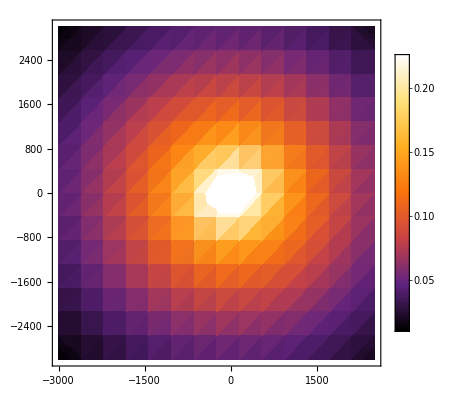

```mathematica
DensityPlot[ConcCyl[{x,y},{1,0.01},{0.1,3000 √2}],{x,-3000,2500},{y,-3000,3000},ColorFunction->"SunsetColors",PlotLegends-> Automatic]
```

## Using steady state solution to diffusion equation (azimuthal and poloidal symmetry, spherical)

Considering a hollow sphere with inner and outer radii given by a and b. At steady state, the heat equation in spherical coordinates with azimuthal and poloidal symmetry becomes, 
                                      

                                                   ∂/(∂r)(r^2∂/(∂r))=0

```mathematica
soln=DSolve[D[r^2 D[c[r],r],r]== 0,c[r],r]//First
```

{c[r]→-C[1]/r+C[2]}

```mathematica
soln1=Solve[{(Evaluate[c[r]/.soln]/.r-> a)== Cp,(Evaluate[c[r]/.soln]/.r-> b)== Cb},{C[1],C[2]}]//First
```

{C[1]→-(a b (Cb-Cp))/(a-b),C[2]→-(b Cb-a Cp)/(a-b)}

```mathematica
ConcSph[{x_,y_},{Cp_,Cb_},{a_,b_}]=Evaluate[c[r]/.soln/.soln1/.r->√(x^2+y^2)]//FullSimplify
```

(-b Cb+a Cp+(a b (Cb-Cp))/(√(x^2+y^2)))/(a-b)

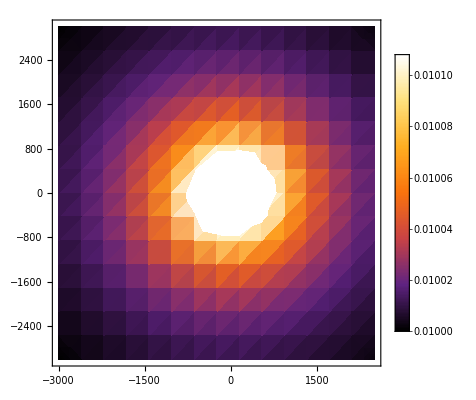

```mathematica
DensityPlot[ConcSph[{x,y},{1,0.01},{0.1,3000 √2}],{x,-3000,2500},{y,-3000,3000},ColorFunction->"SunsetColors",PlotLegends-> Automatic,PlotRange->Automatic,MaxRecursion->10,WorkingPrecision->10]
```

## Chemical walk for Lablets for cylindrical coordinates

### Numerical formulation together with random noise in displacement and noise in sensor opeartions

```mathematica
θR=0;(* maximum random change in angle per time step *)
```

```mathematica
ΔxR=0.;(* maximum random displacement along X per time step *)
```

```mathematica
ΔyR=0.;(* maximum random displacement along Y per time step *)
```

```mathematica
ΔcR=0.1;(* maximun noise noise in sensor measurement *)
```

```mathematica
Δt=0.4;(* Switching times for Lablet, also time step *)
```

```mathematica
dt=0.4;(* time step for simulation *)
```

```mathematica
tT=2000;(* Total time of simulation *)
```

```mathematica
tSteps=tT/dt;
```

```mathematica
vLablet=70.;ωLablet=0.6;α=π/12;
```

```mathematica
ntS=2; (* Number of steps after with switching operation takes place *)
```

```mathematica
nOp=(tT/Δt);
```

#### 1-Bit operation (comparing single threshold value)

```mathematica
simFunc[θR_,ΔxR_,ΔyR_,ΔcR_,cTh_,ntS_,v_,ω_]:=Module[{mType1,mType2},
mType1[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+θR RandomReal[NormalDistribution[0,1]];
X1=X+2v Cos[Θ1]dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+2v Sin[Θ1]dt+ΔyR RandomReal[NormalDistribution[0,1]];
(*If[Y1≤ 0,Y1=0];*)
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
mType2[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+ω dt+θR RandomReal[NormalDistribution[0,1]];
X1=X+v( Cos[Θ](1+Sin[α])-Cos[α]Sin[Θ])dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+v( Cos[α]Cos[Θ]+(1+Sin[α])Sin[Θ])dt+ΔyR RandomReal[NormalDistribution[0,1]];
(*If[Y1≤ 0,Y1=0];*)
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
(* Running simulation *)
iPos={-1000,1000};iθ=π/3;
dataPos={{iPos⟦1⟧,iPos⟦2⟧,iθ}};
dataConc={};

Monitor[For[op=1,op≤nOp,op++,
stSeq1={0}; (* Standard translational sequence *)
stSeq2={1,1};(* Standard rotational sequence *)

seqX1={1};(* Operation for Case : C1 > C2 *)
seqX2={1,1,1,1,1};(* Operation for Case : C1 < C2 *)

X=Last[dataPos]⟦1⟧ ;Y=Last[dataPos]⟦2⟧;Θ=Last[dataPos]⟦3⟧;(* Initializing position and orientation *)

(* Standard translation operation *)
SeqOp=Flatten[ConstantArray[stSeq1⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[stSeq1]]];
ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];

Cm=ConcCyl[{X,Y},{100,0.01},{0.1,3000 √2}]+ΔcR RandomReal[NormalDistribution[0,1]];
If[Mod[op,ntS]== 0,If[Cm-cTh>0,updateSeq=seqX2,updateSeq=stSeq2],updateSeq=stSeq2];
SeqOp=Flatten[ConstantArray[updateSeq⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[updateSeq]]];
ns=1;ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];dataConc=Join[dataConc,{Cm}]],op];
dataConc];
```

#### Adding noise to concentration

```mathematica
dataConc1=simFunc[θR,0,0,0.0,8.5,4,vLablet,ωLablet];
```

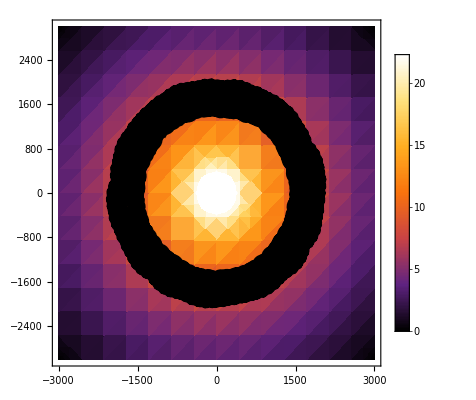

```mathematica
px1=Show[{DensityPlot[ConcCyl[{i,j},{100,0.01},{0.1,3000 √2}],{i,-3000,3000},{j,-3000,3000},ColorFunction->"SunsetColors",PlotRange->{{-3000,3000},{-3000,3000}},MaxRecursion-> 10,PlotLegends->Automatic],ListPlot[dataPos⟦All,1;;2⟧,Joined-> True,AspectRatio-> 1,PlotStyle->Black]},AspectRatio->1]
```

#### 2-Bit operation (comparing two threshold values)

```mathematica
θR=0;(* maximum random change in angle per time step *)
```

```mathematica
ΔxR=0.;(* maximum random displacement along X per time step *)
```

```mathematica
ΔyR=0.;(* maximum random displacement along Y per time step *)
```

```mathematica
ΔcR=0.1;(* maximun noise noise in sensor measurement *)
```

```mathematica
Δt=0.4;(* Switching times for Lablet, also time step *)
```

```mathematica
dt=0.4;(* time step for simulation *)
```

```mathematica
tT=3000;(* Total time of simulation *)
```

```mathematica
tSteps=tT/dt;
```

```mathematica
vLablet=70.;ωLablet=0.6;α=π/12;
```

```mathematica
ntS=2; (* Number of steps after with switching operation takes place *)
```

```mathematica
nOp=(tT/Δt);
```

```mathematica
simFunc[θR_,ΔxR_,ΔyR_,ΔcR_,{cTh1_,cTh2_},ntS_,v_,ω_]:=Module[{mType1,mType2},
mType1[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+θR RandomReal[NormalDistribution[0,1]];
X1=X+2v Cos[Θ1]dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+2v Sin[Θ1]dt+ΔyR RandomReal[NormalDistribution[0,1]];
(*If[Y1≤ 0,Y1=0];*)
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
mType2[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+ω dt+θR RandomReal[NormalDistribution[0,1]];
X1=X+v( Cos[Θ](1+Sin[α])-Cos[α]Sin[Θ])dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+v( Cos[α]Cos[Θ]+(1+Sin[α])Sin[Θ])dt+ΔyR RandomReal[NormalDistribution[0,1]];
(*If[Y1≤ 0,Y1=0];*)
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
(* Running simulation *)
iPos={-1000,1000};iθ=π/3;
dataPos={{iPos⟦1⟧,iPos⟦2⟧,iθ}};
dataConc={};

Monitor[For[op=1,op≤nOp,op++,
stSeq1={0}; (* Standard translational sequence *)
stSeq2={1,1};(* Standard rotational sequence *)

seqX1={1,1,1,1,1};(* Operation for Case : C1 > C2 *)
seqX2={1,1,1,1,1,1,1};(* Operation for Case : C1 < C2 *)

X=Last[dataPos]⟦1⟧ ;Y=Last[dataPos]⟦2⟧;Θ=Last[dataPos]⟦3⟧;(* Initializing position and orientation *)

(* Standard translation operation *)
SeqOp=Flatten[ConstantArray[stSeq1⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[stSeq1]]];
ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];

Cm=ConcCyl[{X,Y},{100,0.01},{0.1,3000 √2}]+ΔcR RandomReal[NormalDistribution[0,1]];
If[Mod[op,ntS]== 0,Which[Cm-cTh1>0&&Cm-cTh2<0,updateSeq=seqX1,Cm-cTh2>0,updateSeq=seqX2,Cm-cTh1<0,updateSeq=stSeq2],updateSeq=stSeq2];
SeqOp=Flatten[ConstantArray[updateSeq⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[updateSeq]]];
ns=1;ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];dataConc=Join[dataConc,{Cm}]],op];
dataConc];
```

```mathematica
dataConc1=simFunc[θR,0,0,0.0,{8.5,10},4,vLablet,ωLablet];
```

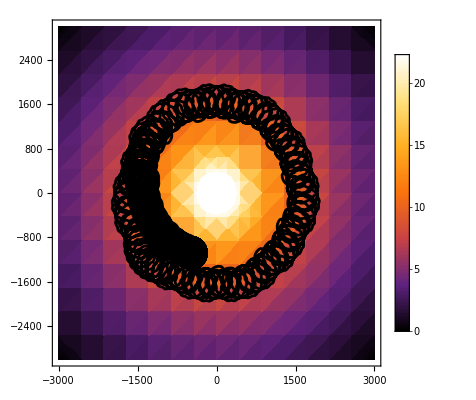

```mathematica
px2=Show[{DensityPlot[ConcCyl[{i,j},{100,0.01},{0.1,3000 √2}],{i,-3000,3000},{j,-3000,3000},ColorFunction->"SunsetColors",PlotRange->{{-3000,3000},{-3000,3000}},MaxRecursion-> 10,PlotLegends->Automatic],ListPlot[dataPos⟦All,1;;2⟧,Joined-> True,AspectRatio-> 1,PlotStyle->Black,PlotRange-> Full]},AspectRatio->1]
```

#### 4 bit logic (defining n threshold values)

```mathematica
θR=0;(* maximum random change in angle per time step *)
```

```mathematica
ΔxR=0.;(* maximum random displacement along X per time step *)
```

```mathematica
ΔyR=0.;(* maximum random displacement along Y per time step *)
```

```mathematica
ΔcR=0.1;(* maximun noise noise in sensor measurement *)
```

```mathematica
Δt=0.4;(* Switching times for Lablet, also time step *)
```

```mathematica
dt=0.4;(* time step for simulation *)
```

```mathematica
tT=3000;(* Total time of simulation *)
```

```mathematica
tSteps=tT/dt;
```

```mathematica
vLablet=70.;ωLablet=0.6;α=π/12;
```

```mathematica
ntS=2; (* Number of steps after with switching operation takes place *)
```

```mathematica
nOp=(tT/Δt);
```

```mathematica
simFunc[θR_,ΔxR_,ΔyR_,ΔcR_,{cTh1_,cTh2_,cTh3_,cTh4_},ntS_,v_,ω_]:=Module[{mType1,mType2},
mType1[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+θR RandomReal[NormalDistribution[0,1]];
X1=X+2v Cos[Θ1]dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+2v Sin[Θ1]dt+ΔyR RandomReal[NormalDistribution[0,1]];
(*If[Y1≤ 0,Y1=0];*)
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
mType2[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+ω dt+θR RandomReal[NormalDistribution[0,1]];
X1=X+v( Cos[Θ](1+Sin[α])-Cos[α]Sin[Θ])dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+v( Cos[α]Cos[Θ]+(1+Sin[α])Sin[Θ])dt+ΔyR RandomReal[NormalDistribution[0,1]];
(*If[Y1≤ 0,Y1=0];*)
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
(* Running simulation *)
iPos={-1000,1000};iθ=π/3;
dataPos={{iPos⟦1⟧,iPos⟦2⟧,iθ}};
dataConc={};

Monitor[For[op=1,op≤nOp,op++,
stSeq1={0}; (* Standard translational sequence *)
stSeq2={1,1};(* Standard rotational sequence *)

seqX1={1,1,1,1,1};(* Operation for Threshold 1 *)
seqX2={1,1,1,1,1,1,1};(* Operation for Threshold 2 *)
seqX3={1,1,1,1,1,1,1,1,1};(* Operation for Threshold 1 *)
seqX4={1,1,1,1,1,1,1,1,1,1,1};(* Operation for Threshold 2 *)

X=Last[dataPos]⟦1⟧ ;Y=Last[dataPos]⟦2⟧;Θ=Last[dataPos]⟦3⟧;(* Initializing position and orientation *)

(* Standard translation operation *)
SeqOp=Flatten[ConstantArray[stSeq1⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[stSeq1]]];
ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];

Cm=ConcCyl[{X,Y},{100,0.01},{0.1,3000 √2}]+ΔcR RandomReal[NormalDistribution[0,1]];
If[Mod[op,ntS]== 0,Which[Cm-cTh1>0&&Cm-cTh2<0,updateSeq=seqX1,
                                                        Cm-cTh2>0&&Cm-cTh3<0,updateSeq=seqX2,
                                                        Cm-cTh3>0&&Cm-cTh4<0,updateSeq=seqX3,
                                                        Cm-cTh4>0,updateSeq=seqX4,Cm-cTh1<0,updateSeq=stSeq2],updateSeq=stSeq2];
SeqOp=Flatten[ConstantArray[updateSeq⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[updateSeq]]];
ns=1;ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];dataConc=Join[dataConc,{Cm}]],op];
dataConc];
```

```mathematica
dataConc1=simFunc[θR,0,0,0.0,{8.5,10,11.5,13},4,vLablet,ωLablet];
```

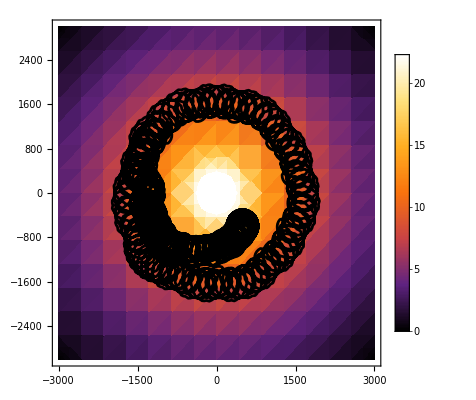

```mathematica
px3=Show[{DensityPlot[ConcCyl[{i,j},{100,0.01},{0.1,3000 √2}],{i,-3000,3000},{j,-3000,3000},ColorFunction->"SunsetColors",PlotRange->{{-3000,3000},{-3000,3000}},MaxRecursion-> 10,PlotLegends->Automatic],ListPlot[dataPos⟦All,1;;2⟧,Joined-> True,AspectRatio-> 1,PlotStyle->Black,PlotRange-> Full]},AspectRatio->1]
```